# MODELS OF JOURNAL CITED

## programs

```mathematica
standerdizeSum[mat_]:=Map[If[Tr[#]>0,#/Tr[#],#]&,mat]
```

```mathematica
journalCitedToMat[jc_]:=Module[
{len,links,crosslinks,linkageTable},
len=Length[jc];
links=Map[Tally[#]&,jc];
crosslinks=Flatten[Table[Map[{n,#[[1]],#[[2]]}&,links[[n]]],{n,Length[links]}],1];
linkageTable=Table[0,{Length[jc]},{Length[jc]}];
Map[(linkageTable[[#[[1]],#[[2]]]]=#[[3]])&,crosslinks];
linkageTable
]
```

## CosDis Vs. Norm Plot

### Not Standerdized

```mathematica
n=200
```

200

```mathematica
tb[n]=Table[RandomReal[],{n},{n}];
```

```mathematica
Graphics[Map[Point[{CosineDistance[Table[1,{n}],#]*20,Norm[#]}]&,tb[n]]]
```

-Graphics-

### Standerdized (table)

```mathematica
n=20
```

20

```mathematica
tb[n]=Table[RandomReal[],{n},{n}];
```

```mathematica
tbST[n]=Map[#/Tr[#]&,tb[n]];
```

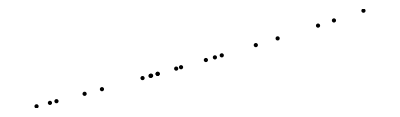

```mathematica
Graphics[Map[Point[{CosineDistance[Table[1,{n}],#],Norm[#]}]&,tbST[n]]]
```

```mathematica
Map[{CosineDistance[Table[1,{n}],#],Norm[#]}&,Map[#/Tr[#]&,Table[RandomReal[],{n},{n}]]]
```

{{0.0892909,0.24553},{0.126499,0.255989},{0.11828,0.253603},{0.104072,0.249581},{0.131109,0.257347},{0.0915888,0.246152},{0.107484,0.250535},{0.0888487,0.245411},{0.0936193,0.246703},{0.0716331,0.24086},{0.117837,0.253476},{0.156325,0.265039},{0.116359,0.253052},{0.144157,0.261271},{0.139199,0.259766},{0.125981,0.255837},{0.0954698,0.247208},{0.0900452,0.245734},{0.128976,0.256717},{0.105579,0.250002}}

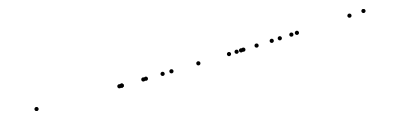

```mathematica
Graphics[Map[Point[{CosineDistance[Table[1,{n}],#],Norm[#]}]&,Map[#/Tr[#]&,Table[RandomReal[],{n},{n}]]]]
```

### Standerdized (array)

```mathematica
n=3
```

3

```mathematica
tb[n]=Table[RandomReal[],{n},{n}];
```

```mathematica
tbST[n]=Map[#/Tr[#]&,tb[n]];
```

```mathematica
Graphics[Map[Point[{CosineDistance[Table[1,{n}],#]*0.1,Norm[#]}]&,tbST[n]]]
```

-Graphics-

```mathematica
Map[{CosineDistance[Table[1,{n}],#]*0.1,Norm[#]}&,Map[#/Tr[#]&,Table[RandomReal[],{n},{n}]]]
```

{{0.00235376,0.591267},{0.00309951,0.595818},{0.000387511,0.579596}}

```mathematica
Map[{CosineDistance[Table[1,{n}],#]*0.1,Norm[#]}&,Map[#/Tr[#]&,Table[RandomReal[],{n},{n}]]]
```

{{0.010076,0.642043},{0.0272961,0.794112},{0.0274638,0.795948}}

```mathematica
Graphics[Map[Point[{CosineDistance[Table[1,{n}],#]*0.1,Norm[#]}]&,Map[#/Tr[#]&,Table[RandomReal[],{n},{n}]]]]
```

-Graphics-

```mathematica
Map[{CosineDistance[Table[1,{n}],#],Norm[#]}&,Map[#/Tr[#]&,Array[a,{n,n}]]]
```

{{1-(a[1,1]/(a[1,1]+a[1,2]+a[1,3])+a[1,2]/(a[1,1]+a[1,2]+a[1,3])+a[1,3]/(a[1,1]+a[1,2]+a[1,3]))/(√3 √(Abs[a[1,1]/(a[1,1]+a[1,2]+a[1,3])]^2+Abs[a[1,2]/(a[1,1]+a[1,2]+a[1,3])]^2+Abs[a[1,3]/(a[1,1]+a[1,2]+a[1,3])]^2)),√(Abs[a[1,1]/(a[1,1]+a[1,2]+a[1,3])]^2+Abs[a[1,2]/(a[1,1]+a[1,2]+a[1,3])]^2+Abs[a[1,3]/(a[1,1]+a[1,2]+a[1,3])]^2)},{1-(a[2,1]/(a[2,1]+a[2,2]+a[2,3])+a[2,2]/(a[2,1]+a[2,2]+a[2,3])+a[2,3]/(a[2,1]+a[2,2]+a[2,3]))/(√3 √(Abs[a[2,1]/(a[2,1]+a[2,2]+a[2,3])]^2+Abs[a[2,2]/(a[2,1]+a[2,2]+a[2,3])]^2+Abs[a[2,3]/(a[2,1]+a[2,2]+a[2,3])]^2)),√(Abs[a[2,1]/(a[2,1]+a[2,2]+a[2,3])]^2+Abs[a[2,2]/(a[2,1]+a[2,2]+a[2,3])]^2+Abs[a[2,3]/(a[2,1]+a[2,2]+a[2,3])]^2)},{1-(a[3,1]/(a[3,1]+a[3,2]+a[3,3])+a[3,2]/(a[3,1]+a[3,2]+a[3,3])+a[3,3]/(a[3,1]+a[3,2]+a[3,3]))/(√3 √(Abs[a[3,1]/(a[3,1]+a[3,2]+a[3,3])]^2+Abs[a[3,2]/(a[3,1]+a[3,2]+a[3,3])]^2+Abs[a[3,3]/(a[3,1]+a[3,2]+a[3,3])]^2)),√(Abs[a[3,1]/(a[3,1]+a[3,2]+a[3,3])]^2+Abs[a[3,2]/(a[3,1]+a[3,2]+a[3,3])]^2+Abs[a[3,3]/(a[3,1]+a[3,2]+a[3,3])]^2)}}

## Zipf Citation Model

### model function

```mathematica
za=0.669646185776694
```

0.669646

```mathematica
zc=207611.33260278852
```

207611.

```mathematica
zipF[rank_]:=1/rank
```

```mathematica
zipFF[rank_,a_,c_]:=c/rank^a
```

```mathematica
200*zipFF[200,za,zc]
```

1.1951×10^6

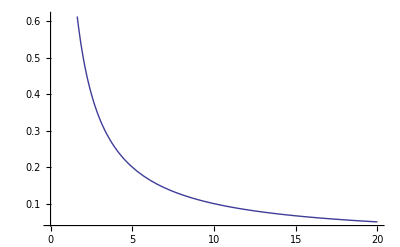

```mathematica
Plot[zipF[n],{n,0,20}]
```

```mathematica
powerLaw[x_,n_,a_]:=n*x^(-a)
```

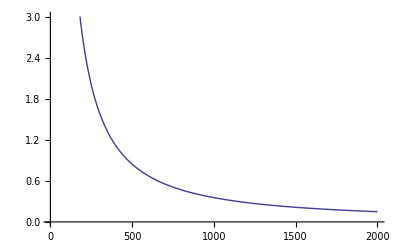

```mathematica
Plot[powerLaw[x,2000,1.25],{x,1,2000}]
```

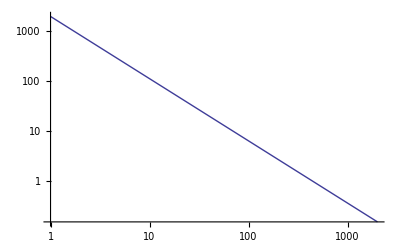

```mathematica
LogLogPlot[powerLaw[x,2000,1.25],{x,1,2000}]
```

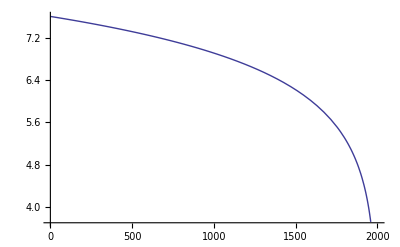

```mathematica
Plot[Log[-x+2000],{x,1,2000}]
```

### application

```mathematica
numOfJournals=2000
```

2000

```mathematica
(*Timing[citedNumOfJournals=Ceiling[Table[numOfJournals*zipF[n],{n,numOfJournals}]//N];]*)
```

```mathematica
Timing[citedNumOfJournals=Ceiling[Table[numOfJournals*zipFF[n,1,1],{n,numOfJournals}]//N];]
```

{0.010999,Null}

```mathematica
(*citedNumOfJournals=Ceiling[Table[zipFF[n,za,zc],{n,numOfJournals}]//N];*)
```

```mathematica
(journalCited=Table[RandomInteger[{1,numOfJournals},citedNumOfJournals[[n]]],{n,numOfJournals}]);
```

```mathematica
linkageTable=journalCitedToMat[journalCited];
```

```mathematica
linkageTableST=standerdizeSum[N[linkageTable]];
```

```mathematica
linkageTableSTaddZero=Append[linkageTableST,Table[0,{numOfJournals}]];
```

```mathematica
linkageTableSTaddZeroPC=PrincipalComponents[linkageTableSTaddZero];
```

```mathematica
linkageTableSTPC=PrincipalComponents[linkageTableST];
```

```mathematica
zipG=Graphics3D[{Map[Point[{#[[1]],#[[2]],#[[3]]}]&,linkageTableSTPC]}]
```

-Graphics3D-

```mathematica
Directory[]
```

/home/kamano

```mathematica
Export["zipf-plot.eps",zipG]
```

zipf-plot.eps

normが一定以上のグループを作る

```mathematica
(topNormPos[0.7]=Position[Map[Norm[N[#]]&,linkageTableST],x_/;x>0.7])//Length
```

1002

```mathematica
cosDistlist[0.7]=Map[CosineDistance[Table[1,{numOfJournals}],#]&,linkageTableST[[Flatten[topNormPos[0.7]]]]];
```

```mathematica
(topNormPos[0.5]=Position[Map[Norm[N[#]]&,linkageTableST],x_/;x>0.5])//Length
```

1334

```mathematica
cosDistlist[0.5]=Map[CosineDistance[Table[1,{numOfJournals}],#]&,linkageTableST[[Flatten[topNormPos[0.5]]]]];
```

```mathematica
(topNormPos[0.4]=Position[Map[Norm[N[#]]&,linkageTableST],x_/;x>0.4])//Length
```

1667

```mathematica
cosDistlist[0.4]=Map[CosineDistance[Table[1,{numOfJournals}],#]&,linkageTableST[[Flatten[topNormPos[0.4]]]]];
```

normの大きなもののみ抽出してもPCAによるplotではスパイクが確認される

```mathematica
Graphics3D[{Map[Point[{#[[1]],#[[2]],#[[3]]}]&,linkageTableSTaddZeroPC[[Flatten[topNormPos[0.7]]]]],RGBColor[0.7,0.5,1],PointSize[0.05],Point[linkageTableSTaddZeroPC[[2001]][[{1,2,3}]]]}]
```

-Graphics3D-

```mathematica
normVSCosDist=Map[{CosineDistance[Table[1,{numOfJournals}],#],Norm[#]}&,linkageTableST];
```

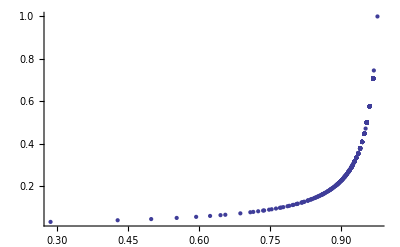

```mathematica
ListPlot[normVSCosDist,PlotRange->All]
```

```mathematica
NSolve[(1-Cos[t])==1,{t}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-1.5708},{t→1.5708}}

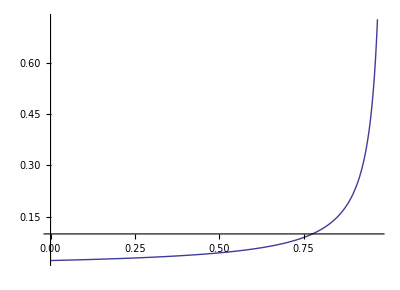

```mathematica
ParametricPlot[{(1-Cos[t]),(Sqrt[2000] Cos[t])^-1},{t,0,1.54},PlotRange->All]
```

elipsoid? pattern plot

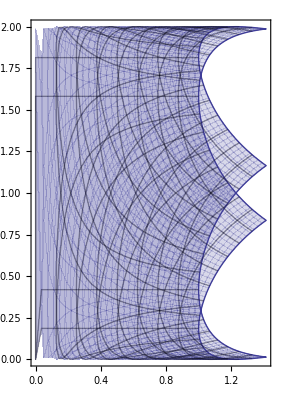

```mathematica
ParametricPlot[{Norm[{a,b}],CosineDistance[{1,1.4},{a,b}]},{a,-1,1},{b,-1,1}]
```

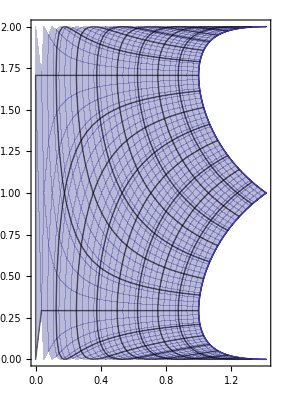

```mathematica
ParametricPlot[{Norm[{a,b}],CosineDistance[{1,1},{a,b}]},{a,-1,1},{b,-1,1}]
```

```mathematica
Manipulate[ParametricPlot[{Norm[{a,b}],CosineDistance[{1,x},{a,b}]},{a,-1,1},{b,-1,1}],{x,0,1}]
```

```mathematica
Manipulate[ParametricPlot[{Norm[{a,b}],CosineDistance[{1,x},{a,b}]},{a,0,1},{b,0,1}],{x,0,1}]
```

```mathematica
Manipulate[ParametricPlot[{Norm[{a,b}],CosineDistance[{y,x}/Tr[{y,x}],{a,b}/Tr[{a,b}]]},{a,0,1},{b,0,1}],{y,0,1},{x,0,1}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

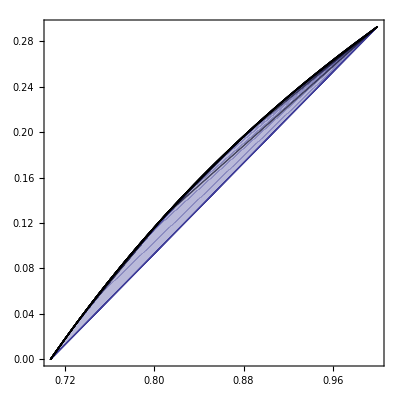

```mathematica
ParametricPlot[{Norm[{a,b}/Tr[{a,b}]],CosineDistance[{0.5,0.5},{a,b}/Tr[{a,b}]]},{a,0,1},{b,0,1}]
```

## Zipf Citation Model (発表用)

### model function

```mathematica
zipFF[rank_,a_,c_]:=c rank^(-a)
```

### application

雑誌数を2000に

```mathematica
numOfJournals=2000
```

2000

```mathematica
(*Timing[citedNumOfJournals=Ceiling[Table[numOfJournals*zipF[n],{n,numOfJournals}]//N];]*)
```

各雑誌の被引用数がzipfの法則に従うとする

```mathematica
Timing[citedNumOfJournals=Ceiling[Table[numOfJournals*zipFF[n,1,1],{n,numOfJournals}]//N];]
```

{0.010998,Null}

```mathematica
(*citedNumOfJournals=Ceiling[Table[zipFF[n,za,zc],{n,numOfJournals}]//N];*)
```

```mathematica
(journalCited=Table[RandomInteger[{1,numOfJournals},citedNumOfJournals[[n]]],{n,numOfJournals}]);
```

```mathematica
linkageTable=journalCitedToMat[journalCited];
```

```mathematica
linkageTableST=standerdizeSum[N[linkageTable]];
```

```mathematica
linkageTableSTaddZero=Append[linkageTableST,Table[0,{numOfJournals}]];
```

```mathematica
linkageTableSTaddZeroPC=PrincipalComponents[linkageTableSTaddZero];
```

```mathematica
linkageTableSTPC=PrincipalComponents[linkageTableST];
```

```mathematica
zipG=Graphics3D[{Map[Point[{#[[1]],#[[2]],#[[3]]}]&,linkageTableSTPC]}]
```

-Graphics3D-

```mathematica
Directory[]
```

/home/kamano

```mathematica
Export["zipf-plot.eps",zipG]
```

zipf-plot.eps

normが一定以上のグループを作る

```mathematica
(topNormPos[0.7]=Position[Map[Norm[N[#]]&,linkageTableST],x_/;x>0.7])//Length
```

1002

```mathematica
cosDistlist[0.7]=Map[CosineDistance[Table[1,{numOfJournals}],#]&,linkageTableST[[Flatten[topNormPos[0.7]]]]];
```

```mathematica
(topNormPos[0.5]=Position[Map[Norm[N[#]]&,linkageTableST],x_/;x>0.5])//Length
```

1334

```mathematica
cosDistlist[0.5]=Map[CosineDistance[Table[1,{numOfJournals}],#]&,linkageTableST[[Flatten[topNormPos[0.5]]]]];
```

```mathematica
(topNormPos[0.4]=Position[Map[Norm[N[#]]&,linkageTableST],x_/;x>0.4])//Length
```

1667

```mathematica
cosDistlist[0.4]=Map[CosineDistance[Table[1,{numOfJournals}],#]&,linkageTableST[[Flatten[topNormPos[0.4]]]]];
```

normの大きなもののみ抽出してもPCAによるplotではスパイクが確認される

```mathematica
Graphics3D[{Map[Point[{#[[1]],#[[2]],#[[3]]}]&,linkageTableSTaddZeroPC[[Flatten[topNormPos[0.7]]]]],RGBColor[0.7,0.5,1],PointSize[0.05],Point[linkageTableSTaddZeroPC[[2001]][[{1,2,3}]]]}]
```

-Graphics3D-

```mathematica
normVSCosDist=Map[{CosineDistance[Table[1,{numOfJournals}],#],Norm[#]}&,linkageTableST];
```

```mathematica
ListPlot[normVSCosDist,PlotRange->All]
```

-Graphics-

```mathematica
NSolve[(1-Cos[t])==1,{t}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-1.5708},{t→1.5708}}

```mathematica
ParametricPlot[{(1-Cos[t]),(Sqrt[2000] Cos[t])^-1},{t,0,1.54},PlotRange->All]
```

-Graphics-

elipsoid? pattern plot

```mathematica
ParametricPlot[{Norm[{a,b}],CosineDistance[{1,1.4},{a,b}]},{a,-1,1},{b,-1,1}]
```

-Graphics-

```mathematica
ParametricPlot[{Norm[{a,b}],CosineDistance[{1,1},{a,b}]},{a,-1,1},{b,-1,1}]
```

-Graphics-

```mathematica
Manipulate[ParametricPlot[{Norm[{a,b}],CosineDistance[{1,x},{a,b}]},{a,-1,1},{b,-1,1}],{x,0,1}]
```

```mathematica
Manipulate[ParametricPlot[{Norm[{a,b}],CosineDistance[{1,x},{a,b}]},{a,0,1},{b,0,1}],{x,0,1}]
```

```mathematica
Manipulate[ParametricPlot[{Norm[{a,b}],CosineDistance[{y,x}/Tr[{y,x}],{a,b}/Tr[{a,b}]]},{a,0,1},{b,0,1}],{y,0,1},{x,0,1}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
ParametricPlot[{Norm[{a,b}/Tr[{a,b}]],CosineDistance[{0.5,0.5},{a,b}/Tr[{a,b}]]},{a,0,1},{b,0,1}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

-Graphics-

## Random Citation Model (dense)

### model function

```mathematica
normDistBase[n_]:=Map[If[#<0,0,#]&,Ceiling[RandomVariate[NormalDistribution[n,Sqrt[n]],n]]]
```

### application

```mathematica
numOfJournals=2000
```

2000

```mathematica
(*citedNumOfJournals=Ceiling[Table[numOfJournals*zipF[n],{n,numOfJournals}]//N];*)
```

```mathematica
(*citedNumOfJournals=Ceiling[Table[zipFF[n,za,zc],{n,numOfJournals}]//N];*)
```

```mathematica
citedNumOfJournals=normDistBase[numOfJournals];
```

```mathematica
(journalCited=Table[RandomInteger[{1,numOfJournals},citedNumOfJournals[[n]]],{n,numOfJournals}]);
```

```mathematica
linkageTable=journalCitedToMat[journalCited];
```

```mathematica
linkageTableST=standerdizeSum[N[linkageTable]];
```

```mathematica
linkageTableSTaddZero=Append[linkageTableST,Table[0,{numOfJournals}]];
```

```mathematica
linkageTableSTaddZeroPC=PrincipalComponents[linkageTableSTaddZero];
```

```mathematica
linkageTableSTPC=PrincipalComponents[linkageTableST];
```

```mathematica
ndG=Graphics3D[{Map[Point[{#[[1]],#[[2]],#[[3]]}]&,linkageTableSTPC]}]
```

-Graphics3D-

```mathematica
Export["ndG.eps",ndG]
```

ndG.eps

```mathematica
Directory[]
```

/home/kamano

normが一定以上のグループを作る

```mathematica
(topNormPos[0.7]=Position[Map[Norm[N[#]]&,linkageTableST],x_/;x>0.7])//Length
```

0

```mathematica
cosDistlist[0.7]=Map[CosineDistance[Table[1,{numOfJournals}],#]&,linkageTableST[[Flatten[topNormPos[0.7]]]]];
```

```mathematica
(topNormPos[0.5]=Position[Map[Norm[N[#]]&,linkageTableST],x_/;x>0.5])//Length
```

0

```mathematica
cosDistlist[0.5]=Map[CosineDistance[Table[1,{numOfJournals}],#]&,linkageTableST[[Flatten[topNormPos[0.5]]]]];
```

```mathematica
(topNormPos[0.4]=Position[Map[Norm[N[#]]&,linkageTableST],x_/;x>0.4])//Length
```

0

```mathematica
cosDistlist[0.4]=Map[CosineDistance[Table[1,{numOfJournals}],#]&,linkageTableST[[Flatten[topNormPos[0.4]]]]];
```

```mathematica
Graphics3D[{Map[Point[{#[[1]],#[[2]],#[[3]]}]&,linkageTableSTaddZeroPC[[Flatten[topNormPos[0.7]]]]],RGBColor[0.7,0.5,1],PointSize[0.05],Point[linkageTableSTaddZeroPC[[2001]][[{1,2,3}]]]}]
```

-Graphics3D-

```mathematica
normVSCosDist=Map[{CosineDistance[Table[1,{numOfJournals}],#],Norm[#]}&,linkageTableST];
```

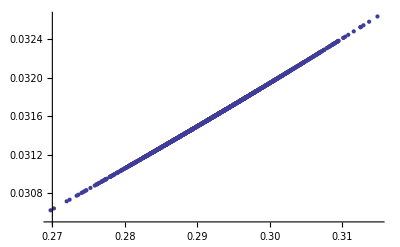

```mathematica
ListPlot[normVSCosDist]
```

## Random Citation Model (sparse 5)

### model function

```mathematica
normDistBase[n_,m_]:=Map[If[#<0,0,#]&,Ceiling[RandomVariate[NormalDistribution[n/m,Sqrt[n/m]],n]]]
```

### application

```mathematica
numOfJournals=2000
```

2000

```mathematica
sparse=5
```

5

```mathematica
(*citedNumOfJournals=Ceiling[Table[numOfJournals*zipF[n],{n,numOfJournals}]//N];*)
```

```mathematica
(*citedNumOfJournals=Ceiling[Table[zipFF[n,za,zc],{n,numOfJournals}]//N];*)
```

```mathematica
citedNumOfJournals=normDistBase[numOfJournals,sparse];
```

```mathematica
(journalCited=Table[RandomInteger[{1,numOfJournals},citedNumOfJournals[[n]]],{n,numOfJournals}]);
```

```mathematica
linkageTable=journalCitedToMat[journalCited];
```

```mathematica
linkageTableST=standerdizeSum[N[linkageTable]];
```

```mathematica
linkageTableSTaddZero=Append[linkageTableST,Table[0,{numOfJournals}]];
```

```mathematica
linkageTableSTaddZeroPC=PrincipalComponents[linkageTableSTaddZero];
```

```mathematica
linkageTableSTPC=PrincipalComponents[linkageTableST];
```

```mathematica
Graphics3D[{Map[Point[{#[[1]],#[[2]],#[[3]]}]&,linkageTableSTPC]}]
```

-Graphics3D-

normが一定以上のグループを作る

```mathematica
(topNormPos[0.7]=Position[Map[Norm[N[#]]&,linkageTableST],x_/;x>0.7])//Length
```

0

```mathematica
cosDistlist[0.7]=Map[CosineDistance[Table[1,{numOfJournals}],#]&,linkageTableST[[Flatten[topNormPos[0.7]]]]];
```

```mathematica
(topNormPos[0.5]=Position[Map[Norm[N[#]]&,linkageTableST],x_/;x>0.5])//Length
```

0

```mathematica
cosDistlist[0.5]=Map[CosineDistance[Table[1,{numOfJournals}],#]&,linkageTableST[[Flatten[topNormPos[0.5]]]]];
```

```mathematica
(topNormPos[0.4]=Position[Map[Norm[N[#]]&,linkageTableST],x_/;x>0.4])//Length
```

0

```mathematica
cosDistlist[0.4]=Map[CosineDistance[Table[1,{numOfJournals}],#]&,linkageTableST[[Flatten[topNormPos[0.4]]]]];
```

```mathematica
Graphics3D[{Map[Point[{#[[1]],#[[2]],#[[3]]}]&,linkageTableSTaddZeroPC[[Flatten[topNormPos[0.7]]]]],RGBColor[0.7,0.5,1],PointSize[0.05],Point[linkageTableSTaddZeroPC[[2001]][[{1,2,3}]]]}]
```

-Graphics3D-

```mathematica
normVSCosDist=Map[{CosineDistance[Table[1,{numOfJournals}],#],Norm[#]}&,linkageTableST];
```

```mathematica
Max[Map[CosineDistance[Table[1,{numOfJournals}],#]&,linkageTableST]]
```

0.623627

```mathematica
Min[Map[CosineDistance[Table[1,{numOfJournals}],#]&,linkageTableST]]
```

0.558881

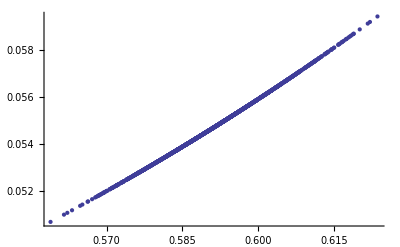

```mathematica
ListPlot[normVSCosDist,PlotRange->All]
```

## Random Citation Model (sparse 10)

### model function

```mathematica
normDistBase[n_,m_]:=Map[If[#<0,0,#]&,Ceiling[RandomVariate[NormalDistribution[n/m,Sqrt[n/m]],n]]]
```

### application

```mathematica
numOfJournals=2000
```

2000

```mathematica
sparse=10
```

10

```mathematica
(*citedNumOfJournals=Ceiling[Table[numOfJournals*zipF[n],{n,numOfJournals}]//N];*)
```

```mathematica
(*citedNumOfJournals=Ceiling[Table[zipFF[n,za,zc],{n,numOfJournals}]//N];*)
```

```mathematica
citedNumOfJournals=normDistBase[numOfJournals,sparse];
```

```mathematica
(journalCited=Table[RandomInteger[{1,numOfJournals},citedNumOfJournals[[n]]],{n,numOfJournals}]);
```

```mathematica
linkageTable=journalCitedToMat[journalCited];
```

```mathematica
linkageTableST=standerdizeSum[N[linkageTable]];
```

```mathematica
linkageTableSTaddZero=Append[linkageTableST,Table[0,{numOfJournals}]];
```

```mathematica
linkageTableSTaddZeroPC=PrincipalComponents[linkageTableSTaddZero];
```

```mathematica
linkageTableSTPC=PrincipalComponents[linkageTableST];
```

```mathematica
Graphics3D[{Map[Point[{#[[1]],#[[2]],#[[3]]}]&,linkageTableSTPC]}]
```

-Graphics3D-

normが一定以上のグループを作る

```mathematica
(topNormPos[0.7]=Position[Map[Norm[N[#]]&,linkageTableST],x_/;x>0.7])//Length
```

0

```mathematica
cosDistlist[0.7]=Map[CosineDistance[Table[1,{numOfJournals}],#]&,linkageTableST[[Flatten[topNormPos[0.7]]]]];
```

```mathematica
(topNormPos[0.5]=Position[Map[Norm[N[#]]&,linkageTableST],x_/;x>0.5])//Length
```

0

```mathematica
cosDistlist[0.5]=Map[CosineDistance[Table[1,{numOfJournals}],#]&,linkageTableST[[Flatten[topNormPos[0.5]]]]];
```

```mathematica
(topNormPos[0.4]=Position[Map[Norm[N[#]]&,linkageTableST],x_/;x>0.4])//Length
```

0

```mathematica
cosDistlist[0.4]=Map[CosineDistance[Table[1,{numOfJournals}],#]&,linkageTableST[[Flatten[topNormPos[0.4]]]]];
```

```mathematica
Graphics3D[{Map[Point[{#[[1]],#[[2]],#[[3]]}]&,linkageTableSTaddZeroPC[[Flatten[topNormPos[0.7]]]]],RGBColor[0.7,0.5,1],PointSize[0.05],Point[linkageTableSTaddZeroPC[[2001]][[{1,2,3}]]]}]
```

-Graphics3D-

```mathematica
normVSCosDist=Map[{CosineDistance[Table[1,{numOfJournals}],#],Norm[#]}&,linkageTableST];
```

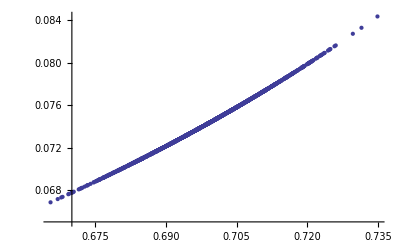

```mathematica
ListPlot[normVSCosDist]
```

## Random Citation Model (sparse 20)

### model function

```mathematica
normDistBase[n_,m_]:=Map[If[#<0,0,#]&,Ceiling[RandomVariate[NormalDistribution[n/m,Sqrt[n/m]],n]]]
```

### application

```mathematica
numOfJournals=2000
```

2000

```mathematica
sparse=20
```

20

```mathematica
(*citedNumOfJournals=Ceiling[Table[numOfJournals*zipF[n],{n,numOfJournals}]//N];*)
```

```mathematica
(*citedNumOfJournals=Ceiling[Table[zipFF[n,za,zc],{n,numOfJournals}]//N];*)
```

```mathematica
citedNumOfJournals=normDistBase[numOfJournals,sparse];
```

```mathematica
(journalCited=Table[RandomInteger[{1,numOfJournals},citedNumOfJournals[[n]]],{n,numOfJournals}]);
```

```mathematica
linkageTable=journalCitedToMat[journalCited];
```

```mathematica
linkageTableST=standerdizeSum[N[linkageTable]];
```

```mathematica
linkageTableSTaddZero=Append[linkageTableST,Table[0,{numOfJournals}]];
```

```mathematica
linkageTableSTaddZeroPC=PrincipalComponents[linkageTableSTaddZero];
```

```mathematica
linkageTableSTPC=PrincipalComponents[linkageTableST];
```

```mathematica
Graphics3D[{Map[Point[{#[[1]],#[[2]],#[[3]]}]&,linkageTableSTPC]}]
```

-Graphics3D-

normが一定以上のグループを作る

```mathematica
(topNormPos[0.7]=Position[Map[Norm[N[#]]&,linkageTableST],x_/;x>0.7])//Length
```

0

```mathematica
cosDistlist[0.7]=Map[CosineDistance[Table[1,{numOfJournals}],#]&,linkageTableST[[Flatten[topNormPos[0.7]]]]];
```

```mathematica
(topNormPos[0.5]=Position[Map[Norm[N[#]]&,linkageTableST],x_/;x>0.5])//Length
```

0

```mathematica
cosDistlist[0.5]=Map[CosineDistance[Table[1,{numOfJournals}],#]&,linkageTableST[[Flatten[topNormPos[0.5]]]]];
```

```mathematica
(topNormPos[0.4]=Position[Map[Norm[N[#]]&,linkageTableST],x_/;x>0.4])//Length
```

0

```mathematica
cosDistlist[0.4]=Map[CosineDistance[Table[1,{numOfJournals}],#]&,linkageTableST[[Flatten[topNormPos[0.4]]]]];
```

```mathematica
Graphics3D[{Map[Point[{#[[1]],#[[2]],#[[3]]}]&,linkageTableSTaddZeroPC[[Flatten[topNormPos[0.7]]]]],RGBColor[0.7,0.5,1],PointSize[0.05],Point[linkageTableSTaddZeroPC[[2001]][[{1,2,3}]]]}]
```

-Graphics3D-

```mathematica
normVSCosDist=Map[{CosineDistance[Table[1,{numOfJournals}],#],Norm[#]}&,linkageTableST];
```

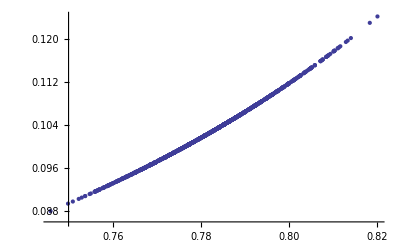

```mathematica
ListPlot[normVSCosDist]
```

## Random Citation Model (sparse 20, wide x2)

### model function

```mathematica
normDistBase[n_,m_]:=Map[If[#<0,0,#]&,Ceiling[RandomVariate[NormalDistribution[n/m,2 Sqrt[n/m]],n]]]
```

### application

```mathematica
numOfJournals=2000
```

2000

```mathematica
sparse=20
```

20

```mathematica
(*citedNumOfJournals=Ceiling[Table[numOfJournals*zipF[n],{n,numOfJournals}]//N];*)
```

```mathematica
(*citedNumOfJournals=Ceiling[Table[zipFF[n,za,zc],{n,numOfJournals}]//N];*)
```

```mathematica
citedNumOfJournals=normDistBase[numOfJournals,sparse];
```

```mathematica
(journalCited=Table[RandomInteger[{1,numOfJournals},citedNumOfJournals[[n]]],{n,numOfJournals}]);
```

```mathematica
linkageTable=journalCitedToMat[journalCited];
```

```mathematica
linkageTableST=standerdizeSum[N[linkageTable]];
```

```mathematica
linkageTableSTaddZero=Append[linkageTableST,Table[0,{numOfJournals}]];
```

```mathematica
linkageTableSTaddZeroPC=PrincipalComponents[linkageTableSTaddZero];
```

```mathematica
linkageTableSTPC=PrincipalComponents[linkageTableST];
```

```mathematica
Graphics3D[{Map[Point[{#[[1]],#[[2]],#[[3]]}]&,linkageTableSTPC]}]
```

-Graphics3D-

normが一定以上のグループを作る

```mathematica
(topNormPos[0.7]=Position[Map[Norm[N[#]]&,linkageTableST],x_/;x>0.7])//Length
```

0

```mathematica
cosDistlist[0.7]=Map[CosineDistance[Table[1,{numOfJournals}],#]&,linkageTableST[[Flatten[topNormPos[0.7]]]]];
```

```mathematica
(topNormPos[0.5]=Position[Map[Norm[N[#]]&,linkageTableST],x_/;x>0.5])//Length
```

0

```mathematica
cosDistlist[0.5]=Map[CosineDistance[Table[1,{numOfJournals}],#]&,linkageTableST[[Flatten[topNormPos[0.5]]]]];
```

```mathematica
(topNormPos[0.4]=Position[Map[Norm[N[#]]&,linkageTableST],x_/;x>0.4])//Length
```

0

```mathematica
cosDistlist[0.4]=Map[CosineDistance[Table[1,{numOfJournals}],#]&,linkageTableST[[Flatten[topNormPos[0.4]]]]];
```

```mathematica
Graphics3D[{Map[Point[{#[[1]],#[[2]],#[[3]]}]&,linkageTableSTaddZeroPC[[Flatten[topNormPos[0.7]]]]],RGBColor[0.7,0.5,1],PointSize[0.05],Point[linkageTableSTaddZeroPC[[2001]][[{1,2,3}]]]}]
```

-Graphics3D-

```mathematica
normVSCosDist=Map[{CosineDistance[Table[1,{numOfJournals}],#],Norm[#]}&,linkageTableST];
```

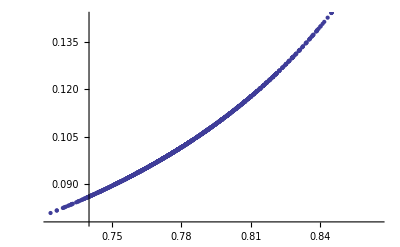

```mathematica
ListPlot[normVSCosDist]
```

## Random matrix model

### Definitions

```mathematica
testMatrix=Table[Random[]*100,{2000},{2000}];
```

```mathematica
maxPositions=Flatten[Map[Position[#,Max[#]][[1]]&,testMatrix]];
```

```mathematica
Length[maxPositions]
```

2000

```mathematica
secondPositions=Flatten[Map[Position[#,Sort[#,Greater][[2]]][[1]]&,testMatrix]];
```

```mathematica
Length[secondPositions]
```

2000

```mathematica
testMatrixRev=Table[
If[
testMatrix[[i]][[i]]>=testMatrix[[i]][[maxPositions[[i]]]],If[secondPositions[[i]]>0,ReplacePart[testMatrix[[i]],i->secondPositions[[i]]]],
testMatrix[[i]]],
{i,2000}];
```

```mathematica
Dimensions[testMatrixRev]
```

{2000,2000}

```mathematica
testMatrix==testMatrixRev
```

True

```mathematica
Table[testMatrix[[i]]==testMatrixRev[[i]],{i,2000}];
```

```mathematica
testRatioMatrix=Map[#/Tr[#]&,testMatrixRev];
```

```mathematica
Map[Tr[#]&,testRatioMatrix];
```

```mathematica
Dimensions[testRatioMatrix]
```

{2000,2000}

```mathematica
Map[Tr[#]&,testRatioMatrix];
```

```mathematica
testRatioMatrixPCA=PrincipalComponents[testRatioMatrix];
```

### Plot

```mathematica
testRatioMatrixPCAPoint[1,2,3]=Map[#[[{1,2,3}]]&,testRatioMatrixPCA];
```

```mathematica
Graphics3D[Map[Point[#]&,testRatioMatrixPCAPoint[1,2,3]]]
```

-Graphics3D-

```mathematica
Map[Norm[#]&,testRatioMatrix];
```

```mathematica
normVSCosDistofRandomMat=Map[{Norm[#],CosineDistance[Table[1,{numOfJournals}],#]}&,testRatioMatrix];
```

```mathematica
Max[Map[#[[1]]&,normVSCosDistofRandomMat]]
```

0.0262032

```mathematica
Min[Map[#[[1]]&,normVSCosDistofRandomMat]]
```

0.0254334

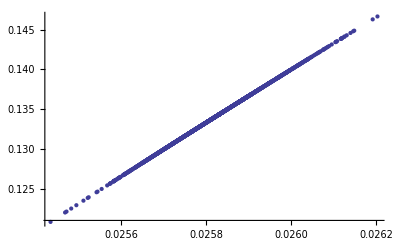

```mathematica
ListPlot[normVSCosDistofRandomMat,PlotRange->All]
```

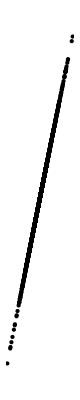

```mathematica
Graphics[Map[Point[#]&,normVSCosDistofRandomMat]]
```

## Exponential Model I

### model function

```mathematica
(E-E^(1-1/rank))/E//Simplify
```

1-ⅇ^(-1/rank)

```mathematica
expF[rank_]:=1-E^(-1/rank)
```

```mathematica
Limit[expF[r],r->0]
```

1

```mathematica
(*expFF[rank_,b_]:=b(E-E^(1-1/rank))*)
```

```mathematica
(*expFF[rank_,b_,s_]:=b(E-E^(1-1/(rank-1+s)))*)
```

```mathematica
expFF[rank_,a_,b_]:=(b*E-E^(1-a/rank))
```

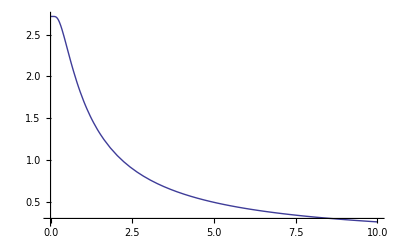

```mathematica
Plot[E expF[x],{x,0,10}]
```

```mathematica
D[expF[x],x]
```

-ⅇ^(-1/x)/x^2

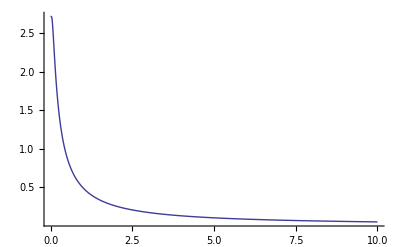

```mathematica
Plot[expFF[x,0.2,1],{x,0,10},PlotRange->All]
```

```mathematica
Limit[expF[x],x->Infinity]
```

0

```mathematica
Limit[expFF[x,1,1],x->Infinity]
```

0

```mathematica
2400*expFF[2400,1,1]//N
```

2.71772

```mathematica
2400*expFF[1,1,1]//N
```

4123.88

### programs

```mathematica
standerdizeSum[mat_]:=Map[If[Tr[#]>0,#/Tr[#],#]&,mat]
```

### application

```mathematica
numOfJournals=2400
```

2400

```mathematica
citedNumOfJournals=Ceiling[Table[1.5*numOfJournals*expF[n],{n,numOfJournals}]//N];
```

```mathematica
(*citedNumOfJournals=Ceiling[Table[numOfJournals*expFF[n,1],{n,numOfJournals}]//N];*)
```

```mathematica
(journalCited=Table[RandomInteger[{1,numOfJournals},citedNumOfJournals[[n]]],{n,numOfJournals}]);
```

```mathematica
links=Map[Tally[#]&,journalCited];
```

```mathematica
crosslinks=Flatten[Table[Map[{n,#[[1]],#[[2]]}&,links[[n]]],{n,Length[links]}],1];
```

```mathematica
linkageTable=Table[0,{numOfJournals},{numOfJournals}];
Map[(linkageTable[[#[[1]],#[[2]]]]=#[[3]])&,crosslinks];
```

```mathematica
linkageTableST=standerdizeSum[N[linkageTable]];
```

```mathematica
linkageTableSTPC=PrincipalComponents[linkageTableST];
```

```mathematica
Graphics3D[{Map[Point[{#[[1]],#[[2]],#[[3]]}]&,linkageTableSTPC]}]
```

-Graphics3D-

## Sigmoid model

### model function

#### Sigmoid

```mathematica
1/(1+E^-x)
```

1/(1+ⅇ^-x)

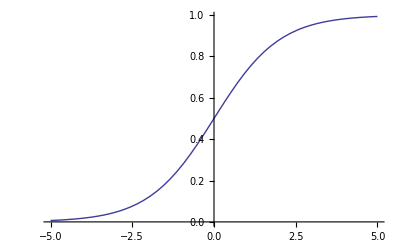

```mathematica
Plot[1/(1+E^-x),{x,-5,5}]
```

#### cited function

```mathematica
1-1/(1+E^-x)
```

1-1/(1+ⅇ^-x)

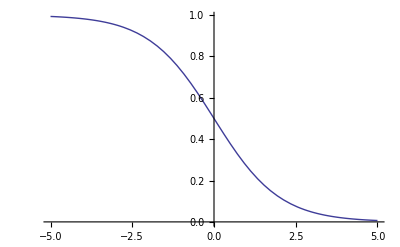

```mathematica
Plot[1-1/(1+E^-(x)),{x,-5,5}]
```

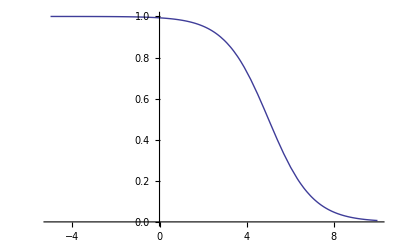

```mathematica
Plot[1-1/(1+E^-(x-5)),{x,-5,10}]
```

## logit model

```mathematica
lgF[maxrank_,a_,b_,rank_]:=E^Log[b(maxrank-b((rank-1)^(a)))]
```

ランクの調整あり ↑

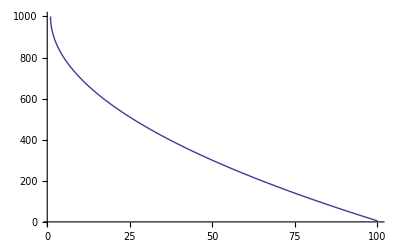

```mathematica
Plot[lgF[100,0.5,10,rank],{rank,1,100}]
```

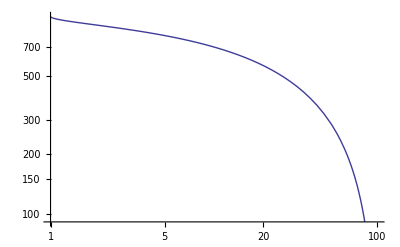

```mathematica
LogLogPlot[lgF[100,0.5,10,rank],{rank,1,100}]
```

## Jornal base - field allocation model

### Package load

```mathematica
(*Needs["MultivariateStatistics`"]*)
```

```mathematica
(*Needs["Histograms`"]*)
```

### Programs

```mathematica
fields[JF_List]:=Union[Flatten[Map[#[[2]]&,JF]]]
```

### Definitions

```mathematica
MaxJournals=10000
```

10000

```mathematica
MaxFields=200
```

200

```mathematica
NJournals=2000
```

2000

```mathematica
NFields=30
```

30

```mathematica
pw=0.5
```

0.5

```mathematica
JournalsAtFieldCoverage[x_]:=NFields/x^pw
```

X : coverage of fields, Y : number of journals.

```mathematica
FieldsAtEachJournal=Ceiling[Table[JournalsAtFieldCoverage[n],{n,1,NJournals}]];
```

```mathematica
FieldsAtEachJournal//Length
```

2000

```mathematica
JournalANDFields=Table[{n,Map[F[#]&,Union[RandomInteger[{1,NFields},FieldsAtEachJournal[[n]]]]]},{n,NJournals}];
```

```mathematica
Length[Intersection[JournalANDFields[[1]][[2]],JournalANDFields[[1]][[2]]]]
```

21

```mathematica
citeweight=jMatrixFieldsIntersectionCount=Outer[Length[Intersection[#1[[2]],#2[[2]]]]&,JournalANDFields,JournalANDFields,1];
```

```mathematica
Dimensions[jMatrixFieldsIntersectionCount]
```

{2000,2000}

```mathematica
Dimensions[citeweight]
```

{2000,2000}

```mathematica
numFieldsOfJournals=Map[Length[#[[2]]]&,JournalANDFields];
```

```mathematica
citeMat=Table[Random[Integer,{1,1000}],{NJournals},{NJournals}];
```

```mathematica
Dimensions[citeMat]
```

{2000,2000}

```mathematica
weightedciteMat=citeMat*citeweight;
```

```mathematica
maxcitedPositions=Flatten[Map[Position[#,Max[#]][[1]]&,weightedciteMat]];
```

```mathematica
secondcitedPositions=Flatten[Map[Position[#,Sort[#,Greater][[2]]][[1]]&,weightedciteMat]];
```

```mathematica
weightedciteMatRev=Table[
If[
weightedciteMat[[i]][[i]]>=weightedciteMat[[i]][[maxcitedPositions[[i]]]],If[secondcitedPositions[[i]]>0,ReplacePart[weightedciteMat[[i]],i->secondcitedPositions[[i]]]],
weightedciteMat[[i]]],
{i,2000}];
```

### Calculation

```mathematica
allFields=fields[JournalANDFields]
```

{F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8],F[9],F[10],F[11],F[12],F[13],F[14],F[15],F[16],F[17],F[18],F[19],F[20],F[21],F[22],F[23],F[24],F[25],F[26],F[27],F[28],F[29],F[30]}

```mathematica
fieldOfjournals=Table[Intersection[{allFields[[l]]},JournalANDFields[[n]][[2]]],{l,Length[allFields]},{n,Length[JournalANDFields]}];
```

```mathematica
Dimensions[fieldOfjournals]
```

{30,2000}

```mathematica
journalsATfield=Table[Flatten[Position[fieldOfjournals[[n]],{_}]],{n,Length[fieldOfjournals]}];
```

```mathematica
numberOFjournalsATfield=Map[Length[#]&,journalsATfield]
```

{103,96,126,120,142,103,126,108,111,107,121,110,107,102,90,111,102,123,113,124,122,108,107,123,97,100,113,118,112,103}

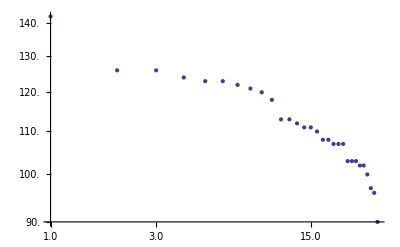

```mathematica
ListLogLogPlot[Sort[numberOFjournalsATfield,Greater]]
```

```mathematica
Tr[numberOFjournalsATfield]
```

3348

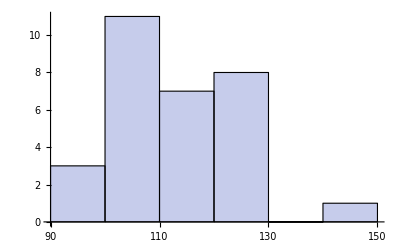

```mathematica
Histogram[Map[Length[#]&,journalsATfield]]
```

### Plot

```mathematica
weightedciteMatRatio=Map[#/Tr[#]&,N[weightedciteMatRev]];
```

```mathematica
Map[Tr[#]&,weightedciteMatRatio];
```

```mathematica
weightedciteMatRatioPCA=PrincipalComponents[weightedciteMatRatio];
```

```mathematica
weightedciteMatRatioPCACoord[1,2,3]=Map[#[[{1,2,3}]]&,weightedciteMatRatioPCA];
```

```mathematica
weightedciteMatRatioPCACoord[1,2,3]//Dimensions
```

{2000,3}

```mathematica
Graphics3D[Map[Point[#]&,weightedciteMatRatioPCACoord[1,2,3]]]
```

-Graphics3D-

## Diagonal square model

```mathematica
fieldSizeFunction[n_,maxsize_,base_]:=Ceiling[maxsize/(base^Range[0,n-1])]
```

```mathematica
fieldSizes=fieldSizeFunction[12,750,1.5]
```

{750,500,334,223,149,99,66,44,30,20,14,9}

```mathematica
totalNumofJournals=Tr[fieldSizes]
```

2238

```mathematica
numofFields=Length[fieldSizes]
```

12

```mathematica
ccweights=Ceiling[fieldSizes^0.5]
```

{28,23,19,15,13,10,9,7,6,5,4,3}

```mathematica
baseRandomMatrix=Table[Random[],{totalNumofJournals},{totalNumofJournals}];
```

```mathematica
baseRandomMatrixOrg=baseRandomMatrix;
```

```mathematica
ccRandomMatrixList=Map[Table[Random[],{#},{#}]&,fieldSizes];
```

```mathematica
ccRandomMatrixDims=Map[Dimensions[#]&,ccRandomMatrixList]
```

{{750,750},{500,500},{334,334},{223,223},{149,149},{99,99},{66,66},{44,44},{30,30},{20,20},{14,14},{9,9}}

```mathematica
ccRandomMatrixListWeighted=Table[ccRandomMatrixList[[n]]*ccweights[[n]],{n,numofFields}];
```

```mathematica
Length[ccRandomMatrixListWeighted]
```

12

```mathematica
Map[Dimensions[#]&,ccRandomMatrixListWeighted]
```

{{750,750},{500,500},{334,334},{223,223},{149,149},{99,99},{66,66},{44,44},{30,30},{20,20},{14,14},{9,9}}

```mathematica
ccRandomMatrixInsertStartPosition=Drop[Prepend[Table[Apply[Plus,ccRandomMatrixDims[[Range[n]]]],{n,numofFields}],{0,0}]+1,-1]
```

{{1,1},{751,751},{1251,1251},{1585,1585},{1808,1808},{1957,1957},{2056,2056},{2122,2122},{2166,2166},{2196,2196},{2216,2216},{2230,2230}}

```mathematica
Length[ccRandomMatrixInsertStartPosition]
```

12

```mathematica
ccRandomMatrixInsertEndPosition=Table[Apply[Plus,ccRandomMatrixDims[[Range[n]]]],{n,numofFields}]
```

{{750,750},{1250,1250},{1584,1584},{1807,1807},{1956,1956},{2055,2055},{2121,2121},{2165,2165},{2195,2195},{2215,2215},{2229,2229},{2238,2238}}

```mathematica
Length[ccRandomMatrixInsertEndPosition]
```

12

```mathematica
(insertRowsStartEnd=Table[ccRandomMatrixInsertStartPosition[[n]][[1]];;ccRandomMatrixInsertEndPosition[[n]][[1]],{n,numofFields}])//MatrixForm
```

(1;;750
751;;1250
1251;;1584
1585;;1807
1808;;1956
1957;;2055
2056;;2121
2122;;2165
2166;;2195
2196;;2215
2216;;2229
2230;;2238)

```mathematica
(insertColumnsStartEnd=Table[ccRandomMatrixInsertStartPosition[[n]][[2]];;ccRandomMatrixInsertEndPosition[[n]][[2]],{n,numofFields}])//MatrixForm
```

(1;;750
751;;1250
1251;;1584
1585;;1807
1808;;1956
1957;;2055
2056;;2121
2122;;2165
2166;;2195
2196;;2215
2216;;2229
2230;;2238)

```mathematica
baseRandomMatrix[[insertRowsStartEnd[[1]],insertColumnsStartEnd[[1]]]]//Dimensions
```

{750,750}

```mathematica
ArrayPlot[baseRandomMatrix]
```

-Graphics-

```mathematica
baseRandomMatrix[[insertRowsStartEnd[[12]],insertColumnsStartEnd[[12]]]]=ccRandomMatrixListWeighted[[12]];
```

```mathematica
i=0;Do[i++;
baseRandomMatrix[[insertRowsStartEnd[[i]],insertColumnsStartEnd[[i]]]]=ccRandomMatrixListWeighted[[i]],
{12}]
```

```mathematica
ArrayPlot[baseRandomMatrix]
```

-Graphics-

```mathematica
baseRandomMatrixRatio=Map[#/Tr[#]&,baseRandomMatrix];
```

```mathematica
Map[Tr[#]&,baseRandomMatrixRatio]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
baseRandomMatrixRatioPCA=PrincipalComponents[baseRandomMatrixRatio];
```

```mathematica
baseRandomMatrixRatioPCAAxes[1,2,3]=Map[{#[[1]],#[[2]],#[[3]]}&,baseRandomMatrixRatioPCA];
```

```mathematica
baseRandomMatrixRatioPCAAxisPoints[1,2,3]=Map[Point[{#[[1]],#[[2]],#[[3]]}]&,baseRandomMatrixRatioPCA];
```

```mathematica
Graphics3D[baseRandomMatrixRatioPCAAxisPoints[1,2,3]]
```

-Graphics3D-

## Test

```mathematica
Norm[{1/2,1/2}]
```

1/(√2)

```mathematica
Norm[Table[1/m,{m}]]/.m->7
```

Table::iterb: Iterator {m} does not have appropriate bounds.

1/(√7)

```mathematica
EuclideanDistance[{1/n,1/n,1/n},{1/m,1/m,0}]
```

√(2 Abs[-1/m+1/n]^2+1/Abs[n]^2)

```mathematica
EuclideanDistance[{1/n,1/n,1/n,1/n},{1/m,1/m,0,1/m}]
```

√(3 Abs[-1/m+1/n]^2+1/Abs[n]^2)

```mathematica
EuclideanDistance[{1/n,1/n,1/n,1/n},{1/m,1/m,0,1/m}]
```

```mathematica
NSum[(1/n)^2,{n}]
```

1.64493

```mathematica
Sum[(1/m)^2,{m}]/.m->3
```

5/4-π^2/6

```mathematica
EuclideanDistance[{a,b,c},{d,e,f}]
```

√(Abs[a-d]^2+Abs[b-e]^2+Abs[c-f]^2)

```mathematica
EuclideanDistance[{1/n,1/n,1/n,1/n},{0,0,0,1}]
```

√(Abs[-1+1/n]^2+3/Abs[n]^2)

```mathematica
r[n_]:=Sqrt[(n-1)(1/n-1/(n-1))^2+(1/n)^2]
```

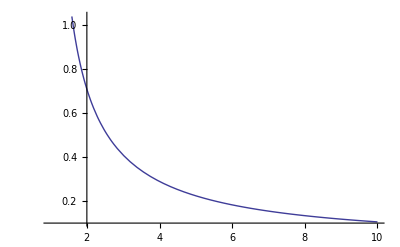

```mathematica
Plot[r[n],{n,1,10}]
```

```mathematica
p[n_]:=Sqrt[(n-1)(1/n)^2+(1/n-1)^2]
```

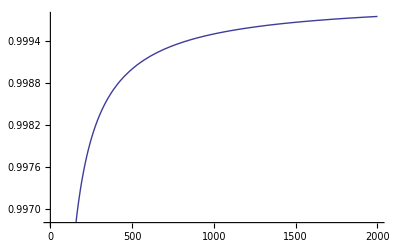

```mathematica
Plot[p[n],{n,1,2000}]
```